```mathematica
Needs["VisualizeGenome`"]
Needs["BSFHistory`"]
```

```mathematica
convertGPATGenome[{"atan"["gauss"["plus"[0.2534219065387728 x0,4.630118948088606,-3.3017315841480586 x0,3.5686227847827148 x0],1]]}]
```

{ArcTan[ⅇ^(-(5.63012+0.520313 x0)^2)]}

```mathematica
listBSF["~/java/exp/GPAT3D_H_H2_200/run_002_130_GENOMES_MATH.txt"]
```

{96477,96373,{times[times[plus[0.999996 times[1,x2,x1,x0,x1],-0.00197473 x2,4.54093 times[plus[3.72673 x0,-3.5065 x0],x1,x2,1],-0.278508 sin[x2],-1.00493 x1],1]]},0.989232}

```mathematica
(evo1=listBSFEvolution["~/java/exp/GPAT3D_H_H2_200/run_002_130_GENOMES_MATH.txt"])//MatrixForm
```

ReplaceAll::reps: {BSFHistory`Private`rules$901} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::write: Tag Span in {times → "times", plus → "plus", sin → "sin", cos → "cos", atan → "atan", gauss → "gauss"} ;; {{{1, -1, {plus}, 1.44591×10^-7}, {2, -1, {plus}, 1.44591×10^-7}, {3, -1, {plus}, 1.44591×10^-7}, {4, -1, {plus}, 1.44591×10^-7}, {5, -1, {plus}, 1.44591×10^-7}, {6, -1, {plus}, 1.44591×10^-7}, {7, -1, {plus}, 1.44591×10^-7}, {8, -1, {plus}, 1.44591×10^-7}, « 36 », {45, -1, {plus}, 1.44591×10^-7}, {46, -1, {plus}, 1.44591×10^-7}, {47, -1, {plus}, 1.44591×10^-7}, {48, -1, {plus}, 1.44591×10^-7}, {49, -1, {plus}, 1.44591×10^-7}, {50, -1, {plus}, 1.44591×10^-7}, « 50 »}, {« 1 »}, « 47 », {« 1 »}, « 915 »} is Protected.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

ReplaceAll::reps: {{{{1, -1, {plus}, 1.44591×10^-7}, {2, -1, {plus}, 1.44591×10^-7}, {3, -1, {plus}, 1.44591×10^-7}, {4, -1, {plus}, 1.44591×10^-7}, {5, -1, {plus}, 1.44591×10^-7}, {6, -1, {plus}, 1.44591×10^-7}, {7, -1, {plus}, 1.44591×10^-7}, {8, -1, {plus}, 1.44591×10^-7}, {9, -1, {plus}, 1.44591×10^-7}, « 34 », {44, -1, {plus}, 1.44591×10^-7}, {45, -1, {plus}, 1.44591×10^-7}, {46, -1, {plus}, 1.44591×10^-7}, {47, -1, {plus}, 1.44591×10^-7}, {48, -1, {plus}, 1.44591×10^-7}, {49, -1, {plus}, 1.44591×10^-7}, {50, -1, {plus}, 1.44591×10^-7}, « 50 »}, « 49 », « 915 »}/. (« 1 »)}
 is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

(1 | 12 | -1 | {plus} | 1.44591×10^-7
2 | 130 | 12 | {plus[1. x0]} | 1.4459×10^-7
3 | 288 | 130 | {plus[0.999053]} | 1.44591×10^-7
4 | 348 | 288 | {plus[-4.13378,1. x1]} | 1.44588×10^-7
6 | 562 | 489 | {plus[1.41299,1.00269 x0]} | 1.4459×10^-7
8 | 742 | 646 | {times[1,x0]} | 1.4459×10^-7
10 | 929 | 834 | {times[1,x0,x0]} | 1.44519×10^-7
11 | 1100 | 929 | {times[1,x2,x0]} | 1.48314×10^-7
13 | 1248 | 1198 | {sin[times[1,x2,x0,x0]]} | 1.44591×10^-7
14 | 1395 | 1248 | {plus[1. times[1,x2,x1,x0]]} | 1.4645×10^-7
15 | 1486 | 1395 | {plus[1. times[1,x2,x1,x0,x1]]} | 0.0000113847
19 | 1810 | 1719 | {plus[1.00945 times[1,x2,x1,x0,x1],1. x2]} | 0.0000113006
23 | 2256 | 2177 | {plus[1.00945 times[1,x2,x1,x0,x1],1. x2,1. x1]} | 0.0000112836
122 | 12162 | 12040 | {plus[1.00013 times[1,x2,x1,x0,x1],-0.000298842 x2,-0.961817 x1,1.]} | 0.0000113903
135 | 13457 | 13367 | {plus[1.00013 times[1,x2,x1,x0,x1],-0.000298842 x0,-0.98579 x1,0.995162]} | 0.0000113904
172 | 17118 | 17012 | {plus[1.00013 times[1,x2,x1,x0,x1],-0.00171887 x0,-1.01798 gauss[x1],-0.242195]} | 0.0000113847
173 | 17289 | 17118 | {plus[1.00013 times[1,x2,x1,x0,x1],-0.00171887 x0,-1.05043 times[x1],-0.242195]} | 0.0000113905
176 | 17577 | 17475 | {plus[0.901685 times[1,x2,x1,x0,x1],-0.00171887 x0,-1.05043 times[x1,1],-0.231052]} | 6.50223×10^-6
177 | 17697 | 17577 | {plus[0.902734 times[1,x2,x1,x0,x1],0.0198315 x0,-1.05043 times[x1,1,x0],-0.231052]} | 6.46762×10^-6
183 | 18296 | 18190 | {plus[0.902734 times[1,x2,x1,x0,x1],0.0620517 x0,-0.755242 atan[x1,1,x0],-0.222072]} | 6.56043×10^-6
187 | 18635 | 18531 | {plus[0.902734 times[1,x2,x1,x0,x1],0.0720285 x0,-3.09243 atan[x1,x2,x0],-0.210101]} | 6.59004×10^-6
196 | 19528 | 19415 | {plus[0.91752 times[1,x2,x1,x0,x1],0.211867 x0,2.79752 atan[x2,x2,x0],3.14473]} | 7.44489×10^-6
206 | 20570 | 20470 | {plus[0.978448 times[1,x2,x1,x0,x1],-0.345573 x0,-4.9863 sin[x2,x2,x0],-2.52513]} | 0.0000109856
207 | 20694 | 20570 | {plus[0.978448 times[1,x2,x1,x0,x1],-0.338801 x0,-4.9863 sin[x0,x2,x0],-2.72619]} | 0.0000109853
209 | 20871 | 20761 | {plus[0.999988 times[1,x2,x1,x0,x1],-0.41037 x0,-4.9863 sin[x0,x2,x0,x1],-2.72619]} | 0.0000113872
217 | 21675 | 21584 | {plus[0.999988 times[1,x2,x1,x0,x1],-0.157999 x0,-4.9774 sin[x0,x2,x2,x1],0.199175]} | 0.000011389
222 | 22171 | 22082 | {plus[0.999988 times[1,x2,x1,x0,x1],-0.151082 x0,-4.9774 sin[x0,x2,x2,x1],0.199175,1.00498 x1]} | 0.0000113717
232 | 23183 | 23083 | {plus[0.999988 times[1,x2,x1,x0,x1],-0.177763 x2,-4.57947 sin[x0,x2,x2,x1],0.192155,-1.95226 x1]} | 0.0000113891
267 | 26664 | 26576 | {plus[0.999988 times[1,x2,x1,x0,x1],-0.18443 x2,-4.66186 sin[x0,x1,x2,x1],-0.876965,-1.35558 x1]} | 0.0000113936
279 | 27843 | 27746 | {plus[0.999988 times[1,x2,x1,x0,x1],-0.126676 x2,-4.66186 sin[gauss[x0],x1,x2,x1],4.24857,-0.746102 x1]} | 0.0000113863
280 | 27985 | 27843 | {plus[0.999988 times[1,x2,x1,x0,x1],-0.126676 x2,-4.66186 sin[gauss[x0],x1,x2,1],0.953963,-0.746102 x1]} | 0.0000113882
281 | 28090 | 27985 | {plus[0.999988 times[1,x2,x1,x0,x1],-0.113586 x2,0.630555 gauss[gauss[x0],x1,x2,1],0.953963,-0.746102 x1]} | 0.0000113899
288 | 28721 | 28626 | {plus[0.999988 times[1,x2,x1,x0,x1],-0.113586 x2,0.630555 gauss[atan[x0],x1,x2,1],-0.252711,-0.74039 x1]} | 0.0000113917
296 | 29514 | 29413 | {plus[0.999988 times[1,x2,x1,x0,x1],-2.74317 x2,3.84008 times[atan[x0],x1,x2,1],-0.251691,-0.742154 x1]} | 0.0000754667
304 | 30338 | 30226 | {plus[0.999988 times[1,x2,x1,x0,x1],-2.28228 x2,4.68081 times[atan[x0],x1,x2,1],-4.30226,-4.34664 x0]} | 0.000094464
305 | 30428 | 30338 | {times[plus[0.999988 times[1,x2,x1,x0,x1],-2.29055 x2,4.68081 times[atan[x0],x1,x2,1],-4.33817,-4.34664 x0]]} | 0.0000944462
311 | 31054 | 30951 | {times[plus[0.999988 times[1,x2,x1,x0,x1],-0.121106 x2,4.68602 times[atan[x0],x1,x2,1],-4.33817,-1.26 x0],1]} | 0.000104391
312 | 31180 | 31054 | {times[plus[0.999988 times[1,x2,x1,x0,x1],-0.121106 x2,4.68602 times[atan[x0],x1,x2,1],-4.33292,-1.26 x1],1]} | 0.000105626
320 | 31968 | 31855 | {times[plus[0.999988 times[1,x2,x1,x0,x1],-0.136952 x2,4.68396 times[atan[x0,x0],x1,x2,1],2.01823,-1.26 x1],1]} | 0.0000909901
346 | 34520 | 34421 | {times[plus[0.97529 times[1,x2,x1,x0,x1],-0.0934867 x2,4.56311 times[plus[3.72104 x0,-3.49991 x0],x1,x2,1],-0.657888,-1.25178 x1],1]} | 0.000239168
770 | 76911 | 76805 | {times[plus[0.999774 times[1,x2,x1,x0,x1],-0.00310877 x2,4.54093 times[plus[3.72675 x0,-3.50604 x0],x1,x2,1],0.215023 times[1],-1.0105 x1],1]} | 0.545935
798 | 79782 | 79679 | {times[times[plus[0.999774 times[1,x2,x1,x0,x1],-0.00310877 x2,4.54093 times[plus[3.72673 x0,-3.50604 x0],x1,x2,1],0.215023 times[x2],-1.0105 x1],1]]} | 0.266607
858 | 85785 | 85688 | {times[times[plus[0.999901 times[1,x2,x1,x0,x1],-0.00310877 x2,4.54093 times[plus[3.72673 x0,-3.50604 x0],x1,x2,1],0.167306 atan[x2],-0.99301 x1],1]]} | 0.662782
875 | 87477 | 87387 | {times[times[plus[0.999901 times[1,x2,x1,x0,x1],-0.0158296 x2,4.54093 times[plus[3.72673 x0,-3.5065 x0],x1,x2,1],-0.291342 sin[x2],-0.99301 x1],1]]} | 0.923378
965 | 96477 | 96373 | {times[times[plus[0.999996 times[1,x2,x1,x0,x1],-0.00197473 x2,4.54093 times[plus[3.72673 x0,-3.5065 x0],x1,x2,1],-0.278508 sin[x2],-1.00493 x1],1]]} | 0.989232)

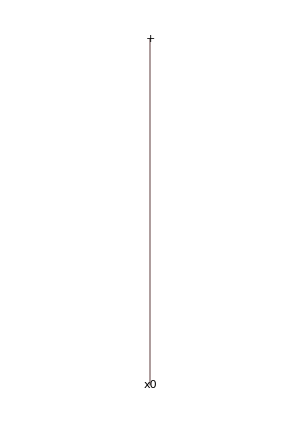
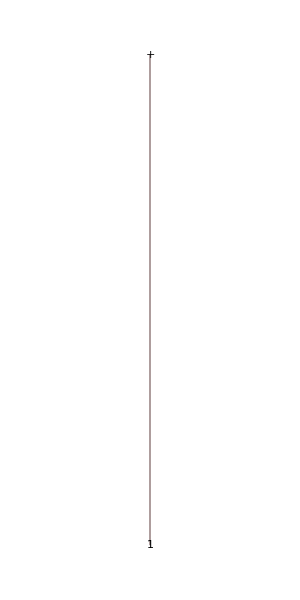
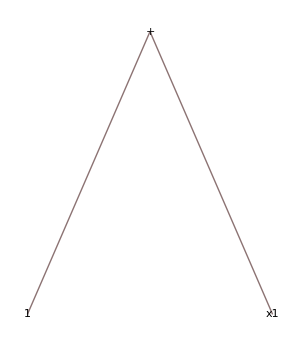
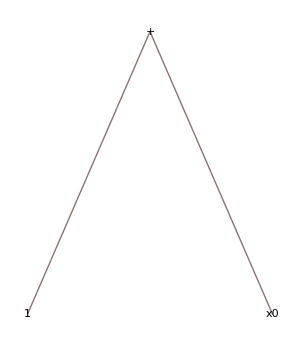
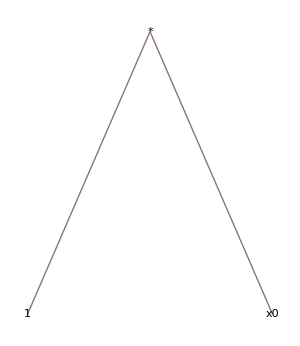
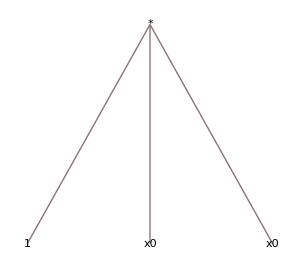
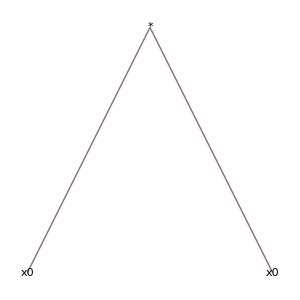
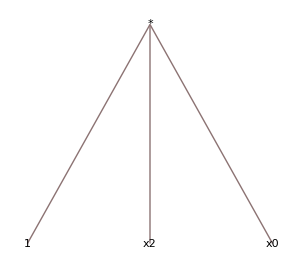
Gen | Genome | Sorted | Simplified | f
1 | -Graphics- | -Graphics- | -Graphics- | 1.44591×10^-7
2 | -Graphics- | -Graphics- | -Graphics- | 1.4459×10^-7
3 | -Graphics- | -Graphics- | -Graphics- | 1.44591×10^-7
4 | -Graphics- | -Graphics- | -Graphics- | 1.44588×10^-7
6 | -Graphics- | -Graphics- | -Graphics- | 1.4459×10^-7
8 | -Graphics- | -Graphics- | -Graphics- | 1.4459×10^-7
10 | -Graphics- | -Graphics- | -Graphics- | 1.44519×10^-7
11 | -Graphics- | -Graphics- | -Graphics- | 1.48314×10^-7
13 | -Graphics- | -Graphics- | -Graphics- | 1.44591×10^-7
14 | -Graphics- | -Graphics- | -Graphics- | 1.4645×10^-7
15 | -Graphics- | -Graphics- | -Graphics- | 0.0000113847
19 | -Graphics- | -Graphics- | -Graphics- | 0.0000113006
23 | -Graphics- | -Graphics- | -Graphics- | 0.0000112836
122 | -Graphics- | -Graphics- | -Graphics- | 0.0000113903
135 | -Graphics- | -Graphics- | -Graphics- | 0.0000113904
172 | -Graphics- | -Graphics- | -Graphics- | 0.0000113847
173 | -Graphics- | -Graphics- | -Graphics- | 0.0000113905
176 | -Graphics- | -Graphics- | -Graphics- | 6.50223×10^-6
177 | -Graphics- | -Graphics- | -Graphics- | 6.46762×10^-6
183 | -Graphics- | -Graphics- | -Graphics- | 6.56043×10^-6
187 | -Graphics- | -Graphics- | -Graphics- | 6.59004×10^-6
196 | -Graphics- | -Graphics- | -Graphics- | 7.44489×10^-6
206 | -Graphics- | -Graphics- | -Graphics- | 0.0000109856
207 | -Graphics- | -Graphics- | -Graphics- | 0.0000109853
209 | -Graphics- | -Graphics- | -Graphics- | 0.0000113872
217 | -Graphics- | -Graphics- | -Graphics- | 0.000011389
222 | -Graphics- | -Graphics- | -Graphics- | 0.0000113717
232 | -Graphics- | -Graphics- | -Graphics- | 0.0000113891
267 | -Graphics- | -Graphics- | -Graphics- | 0.0000113936
279 | -Graphics- | -Graphics- | -Graphics- | 0.0000113863
280 | -Graphics- | -Graphics- | -Graphics- | 0.0000113882
281 | -Graphics- | -Graphics- | -Graphics- | 0.0000113899
288 | -Graphics- | -Graphics- | -Graphics- | 0.0000113917
296 | -Graphics- | -Graphics- | -Graphics- | 0.0000754667
304 | -Graphics- | -Graphics- | -Graphics- | 0.000094464
305 | -Graphics- | -Graphics- | -Graphics- | 0.0000944462
311 | -Graphics- | -Graphics- | -Graphics- | 0.000104391
312 | -Graphics- | -Graphics- | -Graphics- | 0.000105626
320 | -Graphics- | -Graphics- | -Graphics- | 0.0000909901
346 | -Graphics- | -Graphics- | -Graphics- | 0.000239168
770 | -Graphics- | -Graphics- | -Graphics- | 0.545935
798 | -Graphics- | -Graphics- | -Graphics- | 0.266607
858 | -Graphics- | -Graphics- | -Graphics- | 0.662782
875 | -Graphics- | -Graphics- | -Graphics- | 0.923378
965 | -Graphics- | -Graphics- | -Graphics- | 0.989232

```mathematica
showGenomes[evo1]
```

```mathematica
Export["GPAT_H_RUN66.pdf",%]
```

GPAT_H_RUN66.pdf

## 1 D Regression

```mathematica
(evo1=listBSFEvolution["~/java/exp/GPAT1D_G_2/run_001_174_GENOMES_MATH.txt"])//MatrixForm
```

(1 | 17300193 | -1 | {plus} | 2.70569×10^-8
2 | 17300336 | 17300193 | {plus[0.987404]} | 2.70621×10^-8
3 | 17300444 | 17300336 | {plus[0.987404 gauss[1]]} | 2.70588×10^-8
4 | 17300545 | 17300444 | {plus[0.987404 times[1]]} | 2.70621×10^-8
5 | 17300618 | 17300545 | {gauss[plus[0.987404 gauss[1],1.]]} | 2.70577×10^-8
7 | 17300852 | 17300767 | {gauss[plus[0.987404 gauss[1],0.549582,1.3494 x0]]} | 2.70569×10^-8
11 | 17301246 | 17301143 | {gauss[plus[1.82938 gauss[1],-0.878784,4.25122 x0],1]} | 2.70569×10^-8
12 | 17301371 | 17301246 | {times[plus[1.21817 gauss[1],-0.878784,4.24779 x0],1]} | 2.70898×10^-8
14 | 17301559 | 17301465 | {times[plus[1.25431 times[1],-0.865015,4.26333 x0],1]} | 2.70943×10^-8
18 | 17301970 | 17301829 | {times[plus[1.25431 times[1],0.0519364,4.26333 x0],1,x0]} | 2.89265×10^-8
19 | 17302043 | 17301970 | {times[plus[1.25431 times[1,x0],0.052181,4.26333 x0],1,x0]} | 2.94957×10^-8
20 | 17302151 | 17302043 | {times[plus[1.25431 times[1,x0,x0],-0.837428,3.78246 x0],x0,x0]} | 7.4362×10^-7
21 | 17302253 | 17302151 | {times[plus[1.25431 times[1,x0,x0],-0.837428,3.78246 x0],x0,x0,1]} | 7.4362×10^-7
131 | 17313195 | 17313076 | {times[times[plus[1.49973 times[1,x0,x0],-1.14579,2.34657 x0],x0,x0,1]]} | 0.0110484
192 | 17319347 | 17319239 | {plus[1. times[times[plus[1.49986 times[1,x0,x0],-1.15417,2.347 x0],x0,x0,1]]]} | 0.0111279
202 | 17320363 | 17320266 | {plus[1. times[times[plus[1.49986 times[1,x0,x0],-1.15417,2.347 x0],x0,x0,1]],1. x0]} | 0.0120525
362 | 17336319 | 17336198 | {plus[1. times[times[plus[1.49986 times[1,x0,x0],-1.13829,2.32155 x0],x0,x0,1],1],2.1781 x0]} | 0.0388955
428 | 17342956 | 17342831 | {plus[1. times[times[plus[1.49986 times[1,x0,x0],-1.15575,2.29732 x0],x0,x0,1],1],3.93559 x0,1.00118]} | 0.0620225
977 | 17397784 | 17397676 | {plus[1.00023 times[times[plus[1.49986 times[1,x0,x0],-1.11949,2.29902 x0],x0,x0,1],1],3.72859 x0,-4.18753]} | 0.956232)

```mathematica
targetG=1.5*x0^4+2.3*x0^3-1.1*x0^2+3.7*x0-4.5
```

-4.5+3.7 x0-1.1 x0^2+2.3 x0^3+1.5 x0^4

```mathematica
fitness[target_,evolved_]:=
(1/(1+Mean[Table[(target-evolved)^2,{x0,-10,10,20/19}]]))
```

```mathematica
Grid[{Simplify[convertGPATGenome[#][[1]]],
fitness[targetG,convertGPATGenome[#][[1]]]}&/@evo1[[All,4]]]
```

0 | 2.70569×10^-8
0.987404 | 2.70621×10^-8
0.363246 | 2.70588×10^-8
0.987404 | 2.70621×10^-8
0.155916 | 2.70577×10^-8
ⅇ^(-1. (0.912827+1.3494 x0)^2) | 2.70569×10^-8
ⅇ^(-1. (0.794206+4.25122 x0)^2) | 2.70569×10^-8
-0.430645+4.24779 x0 | 2.70898×10^-8
0.38929+4.26333 x0 | 2.70943×10^-8
x0 (1.30624+4.26333 x0) | 2.89265×10^-8
x0 (0.052181+5.51763 x0) | 2.94957×10^-8
x0^2 (-0.837428+3.78246 x0+1.25431 x0^2) | 7.4362×10^-7
x0^2 (-0.837428+3.78246 x0+1.25431 x0^2) | 7.4362×10^-7
x0^2 (-1.14579+2.34657 x0+1.49973 x0^2) | 0.0110484
1. x0^2 (-1.15417+2.347 x0+1.49986 x0^2) | 0.0111279
x0 (1.-1.15417 x0+2.347 x0^2+1.49986 x0^3) | 0.0120525
x0 (2.1781-1.13829 x0+2.32155 x0^2+1.49986 x0^3) | 0.0388955
1.00118+3.93559 x0-1.15575 x0^2+2.29732 x0^3+1.49986 x0^4 | 0.0620225
-4.18753+3.72859 x0-1.11974 x0^2+2.29954 x0^3+1.5002 x0^4 | 0.956232

```mathematica
Manipulate[{fitness[targetG,convertGPATGenome[evo1[[i,4]]][[1]]],Plot[{targetG,convertGPATGenome[evo1[[i,4]]][[1]]},{x0,-10,10},PlotRange->{-150,150},PlotStyle->Thick]},{i,1,Length[evo1],1}]
```